```mathematica
DSolve[{y[x]+α*x^3==-x*y'[x],y[0]==0},y[x],x]
```

{{y[x]→-(x^3 α)/4}}

```mathematica
Clear[y]
```

```mathematica
DSolve[{-x[y]==x'[y]*(y+α*x[y]^3),x[0]==0},x[y],y]
```

DSolve::bvnr: For some branches of the general solution, the given boundary conditions do not restrict the existing freedom in the general solution.

General::stop: Further output of DSolve::bvnr will be suppressed during this calculation.

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

{{x[y]→1/6 (-√2 3^(2/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)))-√2 3^(7/12) √(-((81 3^(1/6) y^4 α^2+3 3^(1/6) α^2 (27 y^4+64 α C[1]^3)+18 3^(2/3) y^2 α √(α^2 (27 y^4+64 α C[1]^3))-72 √3 y^2 α^2 C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3)-24 α C[1] √(α^2 (27 y^4+64 α C[1]^3)) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3)+16 3^(5/6) α^2 C[1]^2 (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)-54 √2 3^(1/6) y^3 α^2 (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)))-6 √2 3^(2/3) y α √(α^2 (27 y^4+64 α C[1]^3)) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3))))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))))))},{x[y]→1/6 (-√2 3^(2/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)))+√2 3^(7/12) √(-((81 3^(1/6) y^4 α^2+3 3^(1/6) α^2 (27 y^4+64 α C[1]^3)+18 3^(2/3) y^2 α √(α^2 (27 y^4+64 α C[1]^3))-72 √3 y^2 α^2 C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3)-24 α C[1] √(α^2 (27 y^4+64 α C[1]^3)) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3)+16 3^(5/6) α^2 C[1]^2 (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)-54 √2 3^(1/6) y^3 α^2 (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)))-6 √2 3^(2/3) y α √(α^2 (27 y^4+64 α C[1]^3)) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3))))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))))))},{x[y]→1/6 (√2 3^(2/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)))-√2 3^(7/12) √(-((81 3^(1/6) y^4 α^2+3 3^(1/6) α^2 (27 y^4+64 α C[1]^3)+18 3^(2/3) y^2 α √(α^2 (27 y^4+64 α C[1]^3))-72 √3 y^2 α^2 C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3)-24 α C[1] √(α^2 (27 y^4+64 α C[1]^3)) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3)+16 3^(5/6) α^2 C[1]^2 (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)+54 √2 3^(1/6) y^3 α^2 (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)))+6 √2 3^(2/3) y α √(α^2 (27 y^4+64 α C[1]^3)) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3))))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))))))},{x[y]→1/6 (√2 3^(2/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)))+√2 3^(7/12) √(-((81 3^(1/6) y^4 α^2+3 3^(1/6) α^2 (27 y^4+64 α C[1]^3)+18 3^(2/3) y^2 α √(α^2 (27 y^4+64 α C[1]^3))-72 √3 y^2 α^2 C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3)-24 α C[1] √(α^2 (27 y^4+64 α C[1]^3)) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3)+16 3^(5/6) α^2 C[1]^2 (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)+54 √2 3^(1/6) y^3 α^2 (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3)))+6 √2 3^(2/3) y α √(α^2 (27 y^4+64 α C[1]^3)) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3) √((9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3))))/(α (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(2/3) (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3))-4 3^(1/3) α C[1] (9 y^2 α+√3 √(α^2 (27 y^4+64 α C[1]^3)))^(1/3))))))}}

```mathematica
Quit[]
```

```mathematica
Eigensystem[{{1,1},{1,2}}]
```

{{1/2 (3+√5),1/2 (3-√5)},{{1/2 (-1+√5),1},{1/2 (-1-√5),1}}}

```mathematica
h[x_]=a*x+b*x^2;
```

```mathematica
eqn = -h[x]+x^2-(h'[x](α*x^2-x*h[x]))
```

-a x+x^2-b x^2-(a+2 b x) (-x (a x+b x^2)+x^2 α)

```mathematica
CoefficientList[eqn,x]
```

{0,-a,1+a^2-b-a α,3 a b-2 b α,2 b^2}

```mathematica
Simplify[Eigenvalues[{{0,-b*c/d},{a*d/b,0}}],Assumptions->{a>0,b>0,c>0,d>0}]
```

{-ⅈ √(a c),ⅈ √(a c)}

```mathematica
a=1; b=2; c=3; d=4;
```

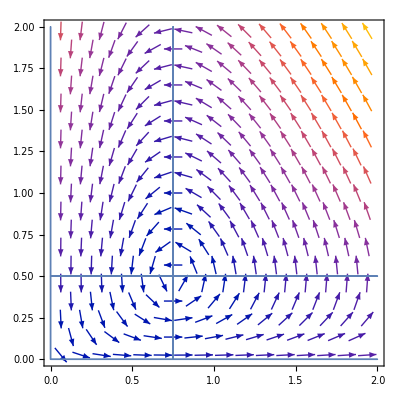

```mathematica
p1=VectorPlot[{x*(a-b*y),y*(-c+d*x)},{x,0,2},{y,0,2}];
p2=ParametricPlot[{x,a/b},{x,0,2},{y,0,2}];
p3=ParametricPlot[{c/d,y},{x,0,2},{y,0,2}];
p4 = ParametricPlot[{x,0},{x,0,2},{y,0,2}];
p5 = ParametricPlot[{0,y},{x,0,2},{y,0,2}];
Show[p1,p2,p3,p4,p5]
```

```mathematica
Clear[a,b,c,d]
```

```mathematica
DSolve[{F'[x]*x/(c-d*x)==C},F[x],x]
```

{{F[x]→C[1]+C (-d x+c Log[x])}}

```mathematica
Reduce[Log[x]<x-1,x]
```

0<x<1||x>1

```mathematica
L[x_,y_]:=C1(c*Log[x]-d*x+a*Log[y]-b*y)+C2
```

```mathematica
cond = Reduce[L[c/d,a/b]==0]
```

C2==a C1+c C1-a C1 Log[a/b]-c C1 Log[c/d]

```mathematica
newL[x_,y_]=L[x,y]/.{C2->a C1+c C1-a C1 Log[a/b]-c C1 Log[c/d]}//Simplify
```

C1 (a+c-d x-b y-a Log[a/b]-c Log[c/d]+c Log[x]+a Log[y])

```mathematica
Reduce[newL[x,y]>=0,C1]
```

$Aborted

```mathematica
Eigensystem[{{2,1},{1,1}}]
```

{{1/2 (3+√5),1/2 (3-√5)},{{1/2 (1+√5),1},{1/2 (1-√5),1}}}

```mathematica
1/2 (3+√5)>1
```

True

```mathematica
Simplify[Solve[-x+b(1+1/a)==x/(a+x^2),x,Reals],Assumptions->{a>0,b<0}]
```

{{x→ConditionalExpression[Root[-a b-a^2 b+(a+a^2) #1+(-b-a b) #1^2+a #1^3&,1], ]},{x→ConditionalExpression[Root[-a b-a^2 b+(a+a^2) #1+(-b-a b) #1^2+a #1^3&,2], ]},{x→ConditionalExpression[Root[-a b-a^2 b+(a+a^2) #1+(-b-a b) #1^2+a #1^3&,3], ]}}

```mathematica
Solve[b/(a+x^2)==x/(a+x^2)]
```

{{x→b}}

```mathematica
Df[x_,y_]={{-1+2x*y,a+x^2},{-2x*y,-a-x^2}};
```

```mathematica
Jac=Df[b,b/(a+b^2)]
```

{{-1+(2 b^2)/(a+b^2),a+b^2},{-(2 b^2)/(a+b^2),-a-b^2}}

```mathematica
Eigenvalues[Jac]
```

{1/(2 (a+b^2))(-a-a^2+b^2-2 a b^2-b^4-√((a+a^2-b^2+2 a b^2+b^4)^2-4 (a^3+3 a^2 b^2+3 a b^4+b^6))),1/(2 (a+b^2))(-a-a^2+b^2-2 a b^2-b^4+√((a+a^2-b^2+2 a b^2+b^4)^2-4 (a^3+3 a^2 b^2+3 a b^4+b^6)))}

```mathematica
Reduce[{Re[1/(2 (a+b^2))(-a-a^2+b^2-2 a b^2-b^4-√((a+a^2-b^2+2 a b^2+b^4)^2-4 (a^3+3 a^2 b^2+3 a b^4+b^6)))]>0,Re[1/(2 (a+b^2))(-a-a^2+b^2-2 a b^2-b^4+√((a+a^2-b^2+2 a b^2+b^4)^2-4 (a^3+3 a^2 b^2+3 a b^4+b^6)))]>0,0<a<=1/8},b,PositiveReals]
```

(0<a<1/64 (71-17 √17)&&Root[a^2-2 a^3+a^4+(-2 a-10 a^2+4 a^3) #1^2+(1-14 a+6 a^2) #1^4+(-6+4 a) #1^6+#1^8&,6]≤b≤Root[a^2-2 a^3+a^4+(-2 a-10 a^2+4 a^3) #1^2+(1-14 a+6 a^2) #1^4+(-6+4 a) #1^6+#1^8&,7])||(a==1/64 (71-17 √17)&&b==Root[a^2-2 a^3+a^4+(-2 a-10 a^2+4 a^3) #1^2+(1-14 a+6 a^2) #1^4+(-6+4 a) #1^6+#1^8&,6])

```mathematica
Det[Jac]//Simplify
```

a+b^2

```mathematica
Tr[Jac]
```

-1-a-b^2+(2 b^2)/(a+b^2)

```mathematica
Reduce[{-1-a-b2+(2 b2)/(a+b2)>0,0<a<=1/8},b2,PositiveReals]
```

0<a<1/8&&-1/2 √(1-8 a)+1/2 (1-2 a)<b2<1/2 √(1-8 a)+1/2 (1-2 a)